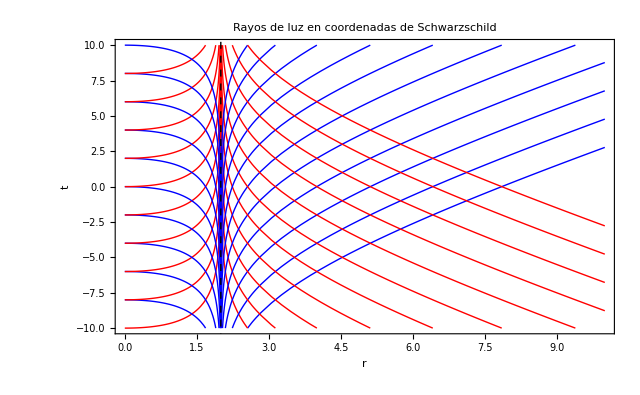

```mathematica
(*Definición de parámetros*)M=1; (*Masa del agujero negro*)
rs=2*M; (*Radio de Schwarzschild*)

(*Coordenada de tortuga r**)
rStar[r_]:=r+rs*Log[Abs[r/rs-1]];

(*Trayectorias de luz en Schwarzschild (t vs r)*)
(*t=constant\pm r**)
plotSchwarzschild=Plot[Evaluate[Table[{rStar[r]+c,-rStar[r]+c},{c,-10,10,2}]],{r,0,10},PlotRange->{{0,10},{-10,10}},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz en coordenadas de Schwarzschild",Epilog->{Dashed,Black,InfiniteLine[{rs,0},{0,1}]}]
```

Horizonte de Cauchy r_- = 0.2

Horizonte de eventos r_+ = 1.

InterpolatingFunction::dmval: Input value {1.00018} lies outside the range of data in the interpolating function. Extrapolation will be used.

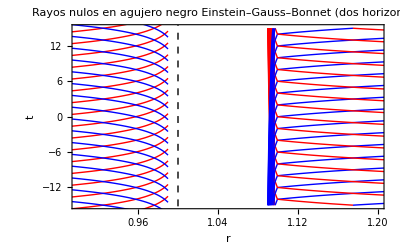

```mathematica
Clear["Global`*"]

(*Parámetros*)
M=0.6;
alpha=0.2;

(*Función métrica Gauss-Bonnet (rama física)*)
f[r_]:=1+r^2/(2 alpha) (1-Sqrt[1+(8 alpha M)/r^3]);

(*Encontrar horizontes*)
roots=r/. NSolve[f[r]==0&&r>0,r];

If[Length[roots]<2,Print["No hay dos horizontes para estos parámetros."];
Abort[]];

rMinus=Min[roots];
rPlus=Max[roots];

Print["Horizonte de Cauchy r_- = ",rMinus];
Print["Horizonte de eventos r_+ = ",rPlus];

(*Construcción de coordenada tortuga por regiones*)

(*Región I:r>r+*)
rStarI=NDSolveValue[{rstar'[r]==1/f[r],rstar[rPlus+0.1]==0},rstar,{r,rPlus+0.1,10}];

(*Región II:r- <r<r+*)
rStarII=NDSolveValue[{rstar'[r]==1/f[r],rstar[(rPlus+rMinus)/2]==0},rstar,{r,rMinus+0.01,rPlus-0.01}];

(*Región III:r<r-*)
rStarIII=NDSolveValue[{rstar'[r]==1/f[r],rstar[rMinus-0.1]==0},rstar,{r,0.05,rMinus-0.1}];

(*Familia de constantes*)
constants=Range[-20,20,2];

(*Gráficos por región*)

plotI=Plot[Evaluate[Table[{rStarI[r]+c,-rStarI[r]+c},{c,constants}]],{r,rPlus,10},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},PlotRange->{{0.9,1.2},{-15,15}}];

plotII=Plot[Evaluate[Table[{rStarII[r]+c,-rStarII[r]+c},{c,constants}]],{r,rMinus+0.01,rPlus-0.01},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];

plotIII=Plot[Evaluate[Table[{rStarIII[r]+c,-rStarIII[r]+c},{c,constants}]],{r,0.05,rMinus-0.1},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]}];

Show[plotI,plotII,Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos nulos en agujero negro Einstein–Gauss–Bonnet (dos horizontes)",Epilog->{Dashed,Black,InfiniteLine[{rPlus,0},{0,1}],InfiniteLine[{rMinus,0},{0,1}]}]
```